# Más cálculos sobre el MH

```mathematica
Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/codigo/CoolTools.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos/usefulFunctions.wl"]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis"]
```

/media/storage/ciencia/investigacion/tesis

## Funciones útiles

```mathematica
(*Cálculo del promedio para cada preimagen:*)
preimageMean[states_List]:= Apply[Plus, states]/Length[states];
```

```mathematica
(*Aplica NumberForm sólo a las entradas de una matriz, no a ella completa.*)
numForm[matrix_, n_]:= Map[NumberForm[#, n]&, matrix, {2}]
```

```mathematica
(*Convierte matriz a sintaxis de LaTeX*)
MatrixToLatex2[matrix_]:=
StringReplace["\\begin{pmatrix}\n"<>
				Fold[(#1<>"\\"<>"\\"<>#2)&, Map[Fold[(ToString[#1]<>"&"<>ToString[#2])&,#]&, matrix]]<>
			  "\n\\end{pmatrix}", "I"->"i"]
```

```mathematica
visualizeMonopartiteSystem[states_List, refState_List]:= Show[Graphics3D[{PointSize[0.015], Blue, Point[densityMatrixToPoint[states, gellMannBasis[1]]]}], 
										Graphics3D[{PointSize[0.015], Red,Point[densityMatrixToPoint[refState, gellMannBasis[1]]]}],
										 Graphics3D[{Opacity[0.3], Sphere[]}]]
```

```mathematica
(*Redefinamos los valores que probaremos:*)
betas ={10,50,100,500,1000};
deltas = {0.001, 0.003, 0.005, 0.007, 0.009, 0.01, 0.03, 0.05, 0.07, 0.1};
rzs = {0, 0.5, 0.8};
swapPs = {0.3, 0.5, 0.8};
```

```mathematica
(*Definimos los estados objetivo apropiadamente:*)
targets = (IdentityMatrix[2] + # PauliMatrix[3])/2 & /@ rzs
```

{{{1/2,0},{0,1/2}},{{0.75,0.},{0.,0.25}},{{0.9,0.},{0.,0.1}}}

```mathematica
(*Lo importamos del archivo donde lo guardamos:*)
initstate = Get["/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/initstate_used_forMH_tests.m"];
initstate//MatrixForm
```

(0.410918+0. ⅈ | 0.227204-0.207377 ⅈ | 0.210585-0.202357 ⅈ | 0.0886308+0.232998 ⅈ
0.227204+0.207377 ⅈ | 0.230281+0. ⅈ | 0.218559-0.00561167 ⅈ | -0.0685809+0.173558 ⅈ
0.210585+0.202357 ⅈ | 0.218559+0.00561167 ⅈ | 0.20757+0. ⅈ | -0.0693191+0.163052 ⅈ
0.0886308-0.232998 ⅈ | -0.0685809-0.173558 ⅈ | -0.0693191-0.163052 ⅈ | 0.151231+0. ⅈ)

```mathematica
(*Definimos la mega lista con todos los parámetros que se ejecutarán:*)
allParams = Flatten[Outer[{#1,#2,#3,#4}&, betas, deltas, swapPs, targets,1],3];
```

```mathematica
Length[allParams]
```

450

```mathematica
allParams[[1]]
```

{10,0.001,0.3,{{1/2,0},{0,1/2}}}

```mathematica
(*función para obtener las posiciones de todas las tuplas de parámetros donde estén involucrados
el target con la swapP indicados en sus argumentos:*)
getParamsPositions[target_, swapP_]:= With[{targetstate=(IdentityMatrix[2]+target PauliMatrix[3])/2},
									  Position[allParams,{_,_,swapP,targetstate},1]]
```

```mathematica
filePath[n_]:= "muestras_MH/gran_test_2/sampleMH_"<>ToString[n]<>".m";
importMHsamples[target_, swapP_]:= Get[filePath[#]]& /@ Select[Flatten@getParamsPositions[target, swapP], (# < 443) &]
```

```mathematica
dist[state_, target_, p_]:= Norm[coarseGraining2[state, p] - target, "Frobenius"]
```

## Importando las muestras del MH

### Para rz = 0

```mathematica
(*Obtenemos las muestras correspondientes a p =0.3: *)
samplesRceroPptoTres = importMHsamples[0, 0.3];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
paramsRceroPptoTres = allParams[[Select[Flatten@getParamsPositions[0, 0.3], (# < 443)&]]];
```

```mathematica
(*Obtenemos las muestras correspondientes a p =0.5: *)
samplesRceroPptoCinco = importMHsamples[0, 0.5];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
(*paramsRceroPptoCinco =  allParams[[Select[Flatten@getParamsPositions[0, 0.5], (# < 172)||(180 < # < 208)&]]];  Este es pal primer test que se hizo*)
paramsRceroPptoCinco = allParams[[Select[Flatten@getParamsPositions[0, 0.5], (# < 443)&]]];
```

```mathematica
(*Obtenemos las muestras correspondientes a p =0.8: *)
samplesRceroPptoOcho = importMHsamples[0, 0.8];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
(*paramsRceroPptoOcho =  allParams[[Select[Flatten@getParamsPositions[0, 0.8], (# < 172)||(180 < # < 208)&]]];*)
paramsRceroPptoOcho = allParams[[Select[Flatten@getParamsPositions[0, 0.8], (# < 443)&]]];
```

```mathematica
Clear[samplesRceroPptoCinco, samplesRceroPptoTres, samplesRceroPptoOcho]
Clear[paramsRceroPptoCinco, paramsRceroPptoTres, paramsRceroPptoOcho]
```

### Para rz = 0.5

```mathematica
(*Obtenemos las muestras correspondientes a p = 0.3: *)
samplesRptoCincoPptoTres = importMHsamples[0.5, 0.3];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
paramsRptoCincoPptoTres =  allParams[[Select[Flatten@getParamsPositions[0.5, 0.3], (# < 172)||(180 < # < 208)&]]];
```

```mathematica
(*Obtenemos las muestras correspondientes a p = 0.5: *)
samplesRptoCincoPptoCinco = importMHsamples[0.5, 0.5];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
paramsRptoCincoPptoCinco = allParams[[Select[Flatten@getParamsPositions[0.5, 0.5], (# < 172)||(180 < # < 208)&]]];
```

```mathematica
(*Obtenemos las muestras correspondientes a p = 0.8: *)
samplesRptoCincoPptoOcho = importMHsamples[0.5, 0.8];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
paramsRptoCincoPptoOcho = allParams[[Select[Flatten@getParamsPositions[0.5, 0.8], (# < 172)||(180 < # < 208)&]]];
```

```mathematica
Clear[samplesRptoCincoPptoCinco, samplesRptoCincoPptoOcho, samplesRptoCincoPptoTres]
Clear[paramsRptoCincoPptoCinco, paramsRptoCincoPptoOcho, paramsRptoCincoPptoTres]
```

### Para rz = 0.8

```mathematica
(*Obtenemos las muestras correspondientes a p = 0.3: *)
samplesRptoOchoPptoTres = importMHsamples[0.8, 0.3];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
paramsRptoOchoPptoTres = allParams[[Select[Flatten@getParamsPositions[0.8, 0.3], (# < 172)||(180 < # < 208)&]]];
```

```mathematica
(*Obtenemos las muestras correspondientes a p = 0.5: *)
samplesRptoOchoPptoCinco = importMHsamples[0.8, 0.5];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
paramsRptoOchoPptoCinco = allParams[[Select[Flatten@getParamsPositions[0.8, 0.5], (# < 172)||(180 < # < 208)&]]];
```

```mathematica
(*Obtenemos las muestras correspondientes a p = 0.8: *)
samplesRptoOchoPptoOcho = importMHsamples[0.8, 0.8];
(*Obtenemos los parámetros que se usaron para obtener esas muestras: *)
paramsRptoOchoPptoOcho = allParams[[Select[Flatten@getParamsPositions[0.8, 0.8], (# < 172)||(180 < # < 208)&]]];
```

## Error en función de δ

### Target rz = 0

#### p = 0.3

```mathematica
dataRceroPptoTres[i_]:= dist[#, targets[[1]], 0.3]& /@ samplesRceroPptoTres[[i,2, 1000;;9000]]
```

```mathematica
errorsRceroPptoTres = Max[#]& /@ Table[dataRceroPptoTres[i],{i,1,50}];
```

```mathematica
groupedErrorsRceroPptoTres = Extract[errorsRceroPptoTres,Position[paramsRceroPptoTres, {#,_,_,_}]]& /@ betas;
```

```mathematica
(*errorDataRceroPptoTres = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRceroPptoTres[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRceroPptoTres[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRceroPptoTres[[5]]}]];*)
errorDataRceroPptoTres = Map[MapThread[List, {deltas, #}]&, groupedErrorsRceroPptoTres];
```

#### p = 0.5

```mathematica
Length[samplesRceroPptoCinco]
```

49

```mathematica
dataRceroPptoCinco[i_]:= dist[#, targets[[1]], 0.5]& /@ samplesRceroPptoCinco[[i,2,1000;;9000]]
```

```mathematica
errorsRceroPptoCinco = Max[#]& /@ Table[dataRceroPptoCinco[i],{i,1,49}];
```

```mathematica
groupedErrorsRceroPptoCinco = Extract[errorsRceroPptoCinco,Position[paramsRceroPptoCinco, {#,_,_,_}]]& /@ betas;
```

```mathematica
(*errorDataRceroPptoCinco = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRceroPptoCinco[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRceroPptoCinco[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRceroPptoCinco[[5]]}]];*)
errorDataRceroPptoCinco = Append[Map[MapThread[List, {deltas, #}]&, groupedErrorsRceroPptoCinco[[1;;4]]], MapThread[List, {deltas[[1;;9]], groupedErrorsRceroPptoCinco[[5]]}]];
```

#### p = 0.8

```mathematica
samplesRceroPptoOcho//Dimensions
```

{49,2}

```mathematica
dataRceroPptoOcho[i_]:= dist[#, targets[[1]], 0.8]& /@ samplesRceroPptoOcho[[i,2,1000;;9000]]
```

```mathematica
errorsRceroPptoOcho = Max[#]& /@ Table[dataRceroPptoOcho[i],{i,1,49}];
```

```mathematica
groupedErrorsRceroPptoOcho = Extract[errorsRceroPptoOcho,Position[paramsRceroPptoOcho, {#,_,_,_}]]& /@ betas;
```

```mathematica
(*errorDataRceroPptoOcho = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRceroPptoOcho[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRceroPptoOcho[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRceroPptoOcho[[5]]}]];*)
errorDataRceroPptoOcho = Append[Map[MapThread[List, {deltas, #}]&, groupedErrorsRceroPptoOcho[[1;;4]]], MapThread[List, {deltas[[1;;9]], groupedErrorsRceroPptoOcho[[5]]}]];
```

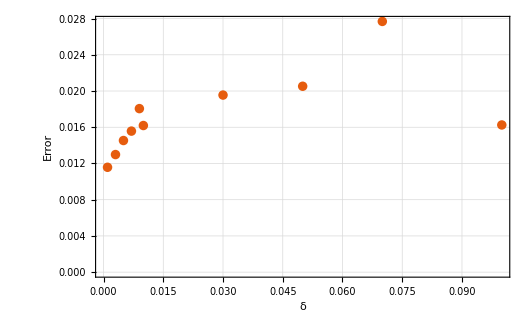
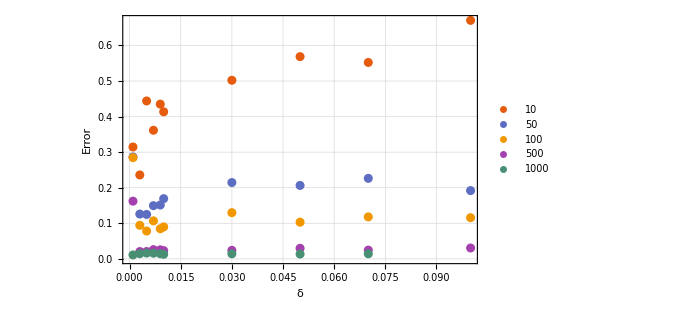
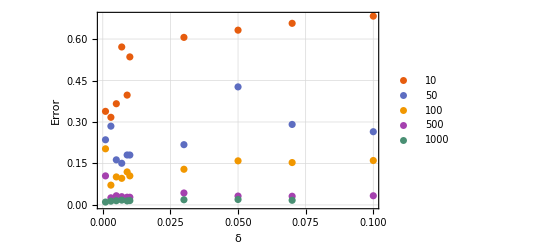

```mathematica
{ListPlot[errorDataRceroPptoTres[[5]], PlotLegends->Automatic, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic],
ListPlot[errorDataRceroPptoCinco, PlotLegends->betas, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic],
ListPlot[errorDataRceroPptoOcho, PlotLegends->betas, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic]
}
```

```mathematica
deltas
```

{0.001,0.003,0.005,0.007,0.009,0.01,0.03,0.05,0.07,0.1}

```mathematica
Length[errorDataRceroPptoTres]
```

5

Se aprecia fácilmente que, conforme aumenta el valor de β, el error en general es menor. Si además, el valor de de δ es pequeño, el error puede disminuir aún más. Podría ser necesario aumentar el número de experimentos para β = 1000, pues en la curva correspondiente se aprecia un aumento del error conforme aumenta δ. Esto no es del todo extraño, pues es normal pensar que si la delta de Dirac es muy estrecha y el paso es grande, las muestras obtenidas no sean tan precisas. Por esta misma razón, obtener esas muestras tarda bastante.

### Target rz = 0.5

#### p = 0.3

```mathematica
dataRptoCincoPptoTres[i_]:= dist[#, targets[[2]], 0.3]& /@ samplesRptoCincoPptoTres[[i,2,1501;;10500]]
```

```mathematica
errorsRptoCincoPptoTres = Max[#]& /@ Table[dataRptoCincoPptoTres[i],{i,1,22}];
```

```mathematica
groupedErrorsRptoCincoPptoTres = Extract[errorsRptoCincoPptoTres,Position[paramsRptoCincoPptoTres, {#,_,_,_}]]& /@ betas;
```

```mathematica
errorDataRptoCincoPptoTres = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRptoCincoPptoTres[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRptoCincoPptoTres[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRptoCincoPptoTres[[5]]}]];
```

#### p = 0.5

```mathematica
dataRptoCincoPptoCinco[i_]:= dist[#, targets[[2]], 0.5]& /@ samplesRptoCincoPptoCinco[[i,2,1501;;10500]]
```

```mathematica
errorsRptoCincoPptoCinco = Max[#]& /@ Table[dataRptoCincoPptoCinco[i],{i,1,22}];
```

```mathematica
groupedErrorsRptoCincoPptoCinco = Extract[errorsRptoCincoPptoCinco,Position[paramsRptoCincoPptoCinco, {#,_,_,_}]]& /@ betas;
```

```mathematica
errorDataRptoCincoPptoCinco = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRptoCincoPptoCinco[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRptoCincoPptoCinco[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRptoCincoPptoCinco[[5]]}]];
```

#### p = 0.8

```mathematica
dataRptoCincoPptoOcho[i_]:= dist[#, targets[[2]], 0.8]& /@ samplesRptoCincoPptoOcho[[i,2,1501;;10500]]
```

```mathematica
errorsRptoCincoPptoOcho = Max[#]& /@ Table[dataRptoCincoPptoOcho[i],{i,1,22}];
```

```mathematica
groupedErrorsRptoCincoPptoOcho = Extract[errorsRptoCincoPptoOcho,Position[paramsRptoCincoPptoOcho, {#,_,_,_}]]& /@ betas;
```

```mathematica
errorDataRptoCincoPptoOcho = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRptoCincoPptoOcho[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRptoCincoPptoOcho[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRptoCincoPptoOcho[[5]]}]];
```

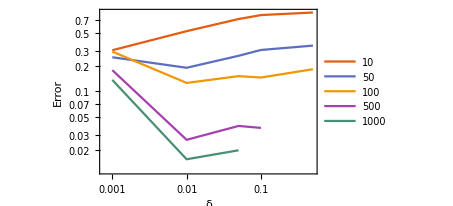
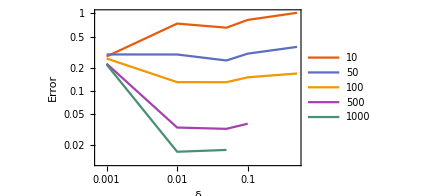
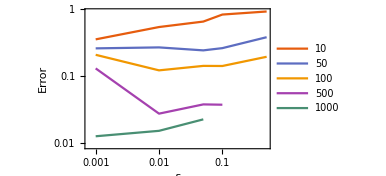

```mathematica
{ListLogLogPlot[errorDataRptoCincoPptoTres, Joined->True, PlotLegends->betas, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic],
ListLogLogPlot[errorDataRptoCincoPptoCinco, Joined->True, PlotLegends->betas, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic],
ListLogLogPlot[errorDataRptoCincoPptoOcho, Joined->True, PlotLegends->betas, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic]
}
```

Aquí se aprecia un comportamiento parecido al de r_z = 0. Nótese, sin embargo, como las curvas parecen partir de un punto en común, fenómeno que se ve más pronunciado para p = 0.5. Aquí también se aprecia el aumento del error cuando δ supera ciertos valores (~ 0.01).

### Target rz = 0.8

#### p = 0.3

```mathematica
dataRptoOchoPptoTres[i_]:= dist[#, targets[[3]], 0.3]& /@ samplesRptoOchoPptoTres[[i,2,1501;;10500]]
```

```mathematica
errorsRptoOchoPptoTres = Max[#]& /@ Table[dataRptoOchoPptoTres[i],{i,1,22}];
```

```mathematica
groupedErrorsRptoOchoPptoTres = Extract[errorsRptoOchoPptoTres,Position[paramsRptoOchoPptoTres, {#,_,_,_}]]& /@ betas;
```

```mathematica
errorDataRptoOchoPptoTres = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRptoOchoPptoTres[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRptoOchoPptoTres[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRptoOchoPptoTres[[5]]}]];
```

#### p = 0.5

```mathematica
dataRptoOchoPptoCinco[i_]:= dist[#, targets[[3]], 0.5]& /@ samplesRptoOchoPptoCinco[[i,2,1501;;10500]]
```

```mathematica
errorsRptoOchoPptoCinco = Max[#]& /@ Table[dataRptoOchoPptoCinco[i],{i,1,22}];
```

```mathematica
groupedErrorsRptoOchoPptoCinco = Extract[errorsRptoOchoPptoCinco,Position[paramsRptoOchoPptoCinco, {#,_,_,_}]]& /@ betas;
```

```mathematica
errorDataRptoOchoPptoCinco = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRptoOchoPptoCinco[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRptoOchoPptoCinco[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRptoOchoPptoCinco[[5]]}]];
```

#### p = 0.8

```mathematica
dataRptoOchoPptoOcho[i_]:= dist[#, targets[[3]], 0.8]& /@ samplesRptoOchoPptoOcho[[i,2,1501;;10500]]
```

```mathematica
errorsRptoOchoPptoOcho = Max[#]& /@ Table[dataRptoOchoPptoOcho[i],{i,1,22}];
```

```mathematica
groupedErrorsRptoOchoPptoOcho = Extract[errorsRptoOchoPptoOcho,Position[paramsRptoOchoPptoOcho, {#,_,_,_}]]& /@ betas;
```

```mathematica
errorDataRptoOchoPptoOcho = Append[
			Append[Map[MapThread[List,{deltas, #}]&, groupedErrorsRptoOchoPptoOcho[[1;;3]]], MapThread[List, {deltas[[1;;4]], groupedErrorsRptoOchoPptoOcho[[4]]}]],
			MapThread[List,{deltas[[1;;3]], groupedErrorsRptoOchoPptoOcho[[5]]}]];
```

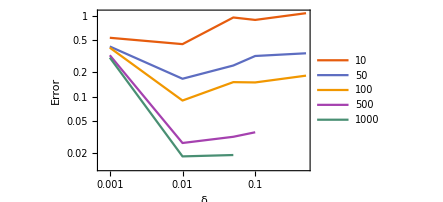
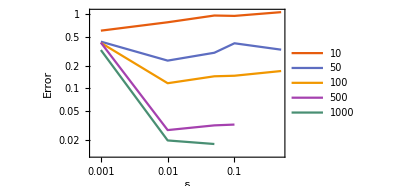
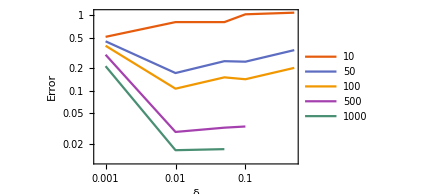

```mathematica
{ListLogLogPlot[errorDataRptoOchoPptoTres, Joined->True, PlotLegends->betas, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic],
ListLogLogPlot[errorDataRptoOchoPptoCinco, Joined->True, PlotLegends->betas, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic],
ListLogLogPlot[errorDataRptoOchoPptoOcho, Joined->True, PlotLegends->betas, FrameLabel->{"δ", "Error"}, PlotTheme->"Scientific", GridLines->Automatic]
}
```

De nuevo lo mismo. Aquí, el fenómeno de las curvas iniciando en un punto común es mucho más notorio. También se aprecia que el error tiende a aumentar en general para valores de δ mayores a 0.01.

## Comparación con el brutal de nuevo

### Importando los datos del brutal

```mathematica
(*Importación de los datos; *)
path = "/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/";
```

```mathematica
(*Para rz = 0:*)
brutalRceroPptoTres = Get[path<>"pureHaarStates_n=10000_p=0.3_rz=0.m"];
brutalRceroPptoCinco = Get[path<>"pureHaarStates_n=10000_p=0.5_rz=0.m"];
brutalRceroPptoOcho = Get[path<>"pureHaarStates_n=10000_p=0.8_rz=0.m"];
```

```mathematica
(*Para rz = 0.5*)
brutalRptoCincoPptoTres = Get[path<>"pureHaarStates_n=10000_p=0.3_rz=0.5.m"];
brutalRptoCincoPptoCinco = Get[path<>"pureHaarStates_n=10000_p=0.5_rz=0.5.m"];
brutalRptoCincoPptoOcho = Get[path<>"pureHaarStates_n=10000_p=0.8_rz=0.5.m"];
```

```mathematica
(*Para rz = 0.8*)
brutalRptoOchoPptoTres = Get[path<>"pureHaarStates_n=10000_p=0.3_rz=0.8.m"];
brutalRptoOchoPptoCinco = Get[path<>"pureHaarStates_n=10000_p=0.5_rz=0.8.m"];
brutalRptoOchoPptoOcho = Get[path<>"pureHaarStates_n=10000_p=0.8_rz=0.8.m"];
```

### Convirtiendo datos a matrices de densidad

```mathematica
(*Convirtiendo a matrices de dnsidad*)
(*Para rz = 0:*)
brutalRceroPptoTres = ketsToDensity[brutalRceroPptoTres];
brutalRceroPptoCinco = ketsToDensity[brutalRceroPptoCinco];
brutalRceroPptoOcho = ketsToDensity[brutalRceroPptoOcho];
(*Para rz = 0.5*)
brutalRptoCincoPptoTres = ketsToDensity[brutalRptoCincoPptoTres];
brutalRptoCincoPptoCinco = ketsToDensity[brutalRptoCincoPptoCinco];
brutalRptoCincoPptoOcho = ketsToDensity[brutalRptoCincoPptoOcho];
(*Para rz = 0.8*)
brutalRptoOchoPptoTres = ketsToDensity[brutalRptoOchoPptoTres];
brutalRptoOchoPptoCinco = ketsToDensity[brutalRptoOchoPptoCinco];
brutalRptoOchoPptoOcho = ketsToDensity[brutalRptoOchoPptoOcho];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRceroPptoTres].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRceroPptoCinco].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRceroPptoOcho].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRptoCincoPptoTres].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRptoCincoPptoCinco].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRptoCincoPptoOcho].

```mathematica
(*Para rz = 0:*)
brutalRceroPptoTres = Drop[brutalRceroPptoTres, 1000];
brutalRceroPptoCinco = Drop[brutalRceroPptoCinco, 1000];
brutalRceroPptoOcho = Drop[brutalRceroPptoOcho, 1000];
(*Para rz = 0.5*)
brutalRptoCincoPptoTres = Drop[brutalRptoCincoPptoTres, 1000];
brutalRptoCincoPptoCinco = Drop[brutalRptoCincoPptoCinco, 1000];
brutalRptoCincoPptoOcho = Drop[brutalRptoCincoPptoOcho, 1000];
(*Para rz = 0.8*)
brutalRptoOchoPptoTres = Drop[brutalRptoOchoPptoTres, 1000];
brutalRptoOchoPptoCinco = Drop[brutalRptoOchoPptoCinco, 1000];
brutalRptoOchoPptoOcho = Drop[brutalRptoOchoPptoOcho, 1000];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRceroPptoTres].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRceroPptoCinco].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRceroPptoOcho].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRptoCincoPptoTres].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRptoCincoPptoCinco].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ketsToDensity[brutalRptoCincoPptoOcho].

### Preimágenes

```mathematica
Grid[{{visualizeBipartiteSystem[brutalRptoOchoPptoTres[[1;;8000]]], visualizeBipartiteSystem[samplesRptoOchoPptoTres[[21,2, 1501;;10500]]]}}]
```

-Graphics3D- | -Graphics3D-

```mathematica
Max[dist[#, targets[[3]], 0.3]& /@ samplesRptoOchoPptoTres[[21,2, 1501;;10500]]]
```

0.0182674

Claramente, algo no está funcionando aquí. A pesar de que el error es 0.01 (al igual que con el brutal), la muestra 21 (para r_z = 0.8 y p = 0.3) resulta muy distinta a simple vista. El error de esos resultados es pequeño, por lo que la explicación de la discordancia resultante debe estar en otro lado. Veamos qué pasa para r_z= 0.8 y p = 0.5:

```mathematica
samplesRptoOchoPptoCinco[[21,2]]//Dimensions
```

{9000,4,4}

```mathematica
(*Densidades de puntos para muestra brutal, y muestras 21 y 19: *)
Grid[{{tripleCylindricalPlot[brutalRptoOchoPptoCinco, targets[[3]], 100,100,100], visualizeBipartiteSystem[brutalRptoOchoPptoCinco]}, 
		{tripleCylindricalPlot[samplesRptoOchoPptoCinco[[21,2]][[1500;;10500]], targets[[3]], 100,100,100], visualizeBipartiteSystem[samplesRptoOchoPptoCinco[[21,2]][[1500;;10500]]]},
		{tripleCylindricalPlot[samplesRptoOchoPptoCinco[[19,2]][[1500;;10500]], targets[[3]], 100,100,100], visualizeBipartiteSystem[samplesRptoOchoPptoCinco[[19,2]][[1500;;10500]]]}}]
```

Transpose::nmtx: The first two levels of {CoolTools`Private`middlePoints[{-0.00340175,0.00277068,0.0089431,0.0151155,0.021288,0.0274604,0.0336328,0.0398052,0.0459777,0.0521501,«93»}],{0.,0.262268,0.102155,0.0843917,0.0882289,0.11063,0.108766,0.100277,0.131492,0.0611802,«92»}} cannot be transposed.

Transpose::nmtx: The first two levels of {CoolTools`Private`middlePoints[{-0.00340175,0.00277068,0.0089431,0.0151155,0.021288,0.0274604,0.0336328,0.0398052,0.0459777,0.0521501,«93»}],{0.,0.0539654,0.0788248,0.121554,0.103739,0.155207,0.137725,0.0957978,0.103072,0.0915542,«92»}} cannot be transposed.

Transpose::nmtx: The first two levels of {CoolTools`Private`middlePoints[{-0.00340175,0.00277068,0.0089431,0.0151155,0.021288,0.0274604,0.0336328,0.0398052,0.0459777,0.0521501,«93»}],{0.,0.262268,0.102155,0.0843917,0.0882289,0.11063,0.108766,0.100277,0.131492,0.0611802,«92»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::take: Cannot take positions 1500 through 10500 in {{{0.411786-2.71051×10^-20 ⅈ,0.227064-0.207573 ⅈ,0.210233-0.202311 ⅈ,0.0889826+0.233513 ⅈ},{0.227064+0.207573 ⅈ,0.229839+2.71051×10^-20 ⅈ,0.217906-0.00558246 ⅈ,-0.068643+0.173616 ⅈ},«1»,{0.0889826-0.233513 ⅈ,-0.068643-0.173616 ⅈ,-0.0692961-0.162935 ⅈ,0.151647-5.42101×10^-20 ⅈ}},«9»,«8990»}.

Part::pkspec1: The expression densityMatrixToPoint[{partialTraceA[1500;;10500],partialTraceB[1500;;10500]},{{{1,0},{0,1}},{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPointPlot3D::ldata: Transpose[densityMatrixToPoint[{partialTraceA[{{{0.411786 - 2.71051 <<1>> I, <<3>>}, <<2>>, {<<4>>}}, <<8999>>}], <<1>>}, {<<4>>}][[<<20>>[<<2>>]]]] is not a valid dataset or list of datasets.

General::stop: Further output of ListPointPlot3D::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPointPlot3D[Transpose[densityMatrixToPoint[{partialTraceA[{{<<4>>}, <<8999>>}], p<<10>>eB[<<1>>]}, {<<4>>}][[<<1>>]]], <<3>>], <<2>>].

Part::take: Cannot take positions 1500 through 10500 in {{{0.480745+3.46945×10^-18 ⅈ,0.216063-0.196375 ⅈ,0.220709-0.179689 ⅈ,0.0778401+0.278071 ⅈ},{0.216063+0.196375 ⅈ,0.177321-4.33681×10^-18 ⅈ,0.172593+0.00939718 ⅈ,-0.0786027+0.15677 ⅈ},«1»,{0.0778401-0.278071 ⅈ,-0.0786027-0.15677 ⅈ,-0.0681989-0.156756 ⅈ,0.173444+0. ⅈ}},{«1»,{«1»},{«1»},«1»},{«1»},«6»,{«1»},«8990»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPointPlot3D[Transpose[densityMatrixToPoint[{partialTraceA[{{<<4>>}, <<8999>>}], p<<10>>eB[<<1>>]}, {<<4>>}][[<<1>>]]], <<3>>], <<2>>].

{-Graphics-,-Graphics-,-Graphics-} | -Graphics3D-
tripleCylindricalPlot[{1}⟦1500;;10500⟧,{{0.9,0.},{0.,0.1}},100,100,100] | Show[ListPointPlot3D[Transpose[densityMatrixToPoint[{partialTraceA[{1}],partialTraceB[{1}]},{{{1,0},{0,1}},{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}]⟦densityMatrixToPoint[{partialTraceA[1500;;10500],partialTraceB[1500;;10500]},{{{1,0},{0,1}},{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}]⟧],BoxRatios→1,PlotStyle→{RGBColor[1, 0, 0],RGBColor[0, 1, 0],PointSize[0.01]},PlotRange→{{-1.,1.},{-1.,1.},{-1.,1.}}],-Graphics3D-,-Graphics3D-]
tripleCylindricalPlot[{1}⟦1500;;10500⟧,{{0.9,0.},{0.,20}},100,100,100] | 1
 |  |  |  |

```mathematica
{paramsRptoOchoPptoCinco[[21]], paramsRptoOchoPptoCinco[[19]]}
```

{{1000,0.01,0.5,{{0.9,0.},{0.,0.1}}},{500,0.1,0.5,{{0.9,0.},{0.,0.1}}}}

```mathematica
{Max[dist[#, targets[[3]], 0.5]& /@ samplesRptoOchoPptoCinco[[21,2]][[1501;;10500]]], Max[dist[#, targets[[3]], 0.5]& /@ samplesRptoOchoPptoCinco[[19,2]][[1501;;10500]]]}
```

{0.0196813,0.0322716}

Los parámteros usados para las muestras 21 y 19 son β = 1000, δ = 0.01 y β = 500, δ = 0.1 respectivamente. Los errores máximos son 0.019 y 0.0322. Sin embargo, la muestra 21 exhibe una distribución de puntos muy extraña, que difiere tanto de la muestra 19 con de la muestra con el brutal. Los estados no tienen problemas al parecer:

```mathematica
PositiveSemidefiniteMatrixQ[U.Chop[samplesRptoOchoPptoCinco[[17,2,116]]].ConjugateTranspose[U]]
```

True

```mathematica
Tr[MatrixPower[U.samplesRptoOchoPptoCinco[[17,2,116]].ConjugateTranspose[U],2]]//Chop
```

1.

```mathematica
PositiveSemidefiniteMatrixQ@samplesRptoOchoPptoCinco[[19,2]][[100]]
```

True

```mathematica
PositiveSemidefiniteMatrixQ[brutalRptoOchoPptoCinco[[1500]]]
```

True

Probablemente, sólo sea que el algoritmo no corrió durante suficiente tiempo